Analiza danych z qc

```mathematica
(*path = "/Users/jakub/Developer/qc/qc/files/";*)
path="/media/Developer/qc/qc/files/";
outNames = FileNames["*", path<>"outputs/lp_channels"];
{files, distances} = Transpose@Table[Transpose@Import[outNames[[i]], "TSV"], {i, 1, Length@outNames}];
{length, visibility} = Transpose@ToExpression[Table[StringSplit[FileNameTake[outNames[[i]]], {"V", "P"}], {i, 1, Length@outNames}]][[All,;;2]];
data =Table[{length[[i]], visibility[[i]], files[[i]], distances[[i]]}, {i, 1, Length@length}];
means = Table[{length[[i]], visibility[[i]], Mean[files[[i]]], Mean[distances[[i]]]},{i,1,Length@length}];
```

```mathematica
firstToEnd[d_]:=AppendTo[d[[2;;]],First@d];
```

```mathematica
ByLength=firstToEnd[firstToEnd[Gather[means, First[#1]==First[#2]&]]]
d =SortBy[Last@ByLength, #[[2]] &]
```

Set::setps: {{{10,0.9,0.335592,1.04884},{10,0.95,0.573449,0.668431},{10,1.,0.957986,0.0655811}},{{11,0.7,0.0190488,1.58712},{11,0.75,0.0407778,1.56207},{11,0.8,0.0827931,1.50873},{11,0.85,0.162587,1.28906},{11,0.9,0.303438,1.09982},{11,1.,0.968607,0.0500997}},{{1,0.9,0.,1.57865},{1,0.95,0.,1.56774},{1,1.,0.,1.56517}},«5»,{{7,0.9,0.439663,0.884202},{7,0.95,0.633342,0.574623},{7,1.,0.908227,0.142901}},{{8,0.9,0.399794,0.947257},{8,0.95,0.610073,0.611065},{8,1.,0.924289,0.118156}},«1»} in the part assignment is not a symbol.

Set::setps: {{{11,0.7,0.0190488,1.58712},{11,0.75,0.0407778,1.56207},{11,0.8,0.0827931,1.50873},{11,0.85,0.162587,1.28906},{11,0.9,0.303438,1.09982},{11,1.,0.968607,0.0500997}},{{1,0.9,0.,1.57865},{1,0.95,0.,1.56774},{1,1.,0.,1.56517}},{{2,0.9,0.148925,1.33945},{2,0.95,0.244577,1.18992},{2,1.,0.278507,1.12954}},«5»,{{8,0.9,0.399794,0.947257},{8,0.95,0.610073,0.611065},{8,1.,0.924289,0.118156}},{{9,0.9,0.36656,0.999925},{9,0.95,0.593563,0.63688},{9,1.,0.941377,0.0917682}},«1»} in the part assignment is not a symbol.

{{{1,0.9,0.,1.57865},{1,0.95,0.,1.56774},{1,1.,0.,1.56517}},{{2,0.9,0.148925,1.33945},{2,0.95,0.244577,1.18992},{2,1.,0.278507,1.12954}},{{3,0.9,0.425794,0.902922},{3,0.95,0.528138,0.742797},{3,1.,0.620659,0.597311}},{{4,0.9,0.476045,0.829565},{4,0.95,0.617605,0.601889},{4,1.,0.762432,0.376436}},{{5,0.9,0.490525,0.806091},{5,0.95,0.641921,0.561748},{5,1.,0.843907,0.246636}},{{6,0.9,0.47863,0.82279},{6,0.95,0.643315,0.559739},{6,1.,0.892704,0.167803}},{{7,0.9,0.439663,0.884202},{7,0.95,0.633342,0.574623},{7,1.,0.908227,0.142901}},{{8,0.9,0.399794,0.947257},{8,0.95,0.610073,0.611065},{8,1.,0.924289,0.118156}},{{9,0.9,0.36656,0.999925},{9,0.95,0.593563,0.63688},{9,1.,0.941377,0.0917682}},{{10,0.9,0.335592,1.04884},{10,0.95,0.573449,0.668431},{10,1.,0.957986,0.0655811}},{{11,0.7,0.0190488,1.58712},{11,0.75,0.0407778,1.56207},{11,0.8,0.0827931,1.50873},{11,0.85,0.162587,1.28906},{11,0.9,0.303438,1.09982},{11,1.,0.968607,0.0500997}}}

{{11,0.7,0.0190488,1.58712},{11,0.75,0.0407778,1.56207},{11,0.8,0.0827931,1.50873},{11,0.85,0.162587,1.28906},{11,0.9,0.303438,1.09982},{11,1.,0.968607,0.0500997}}

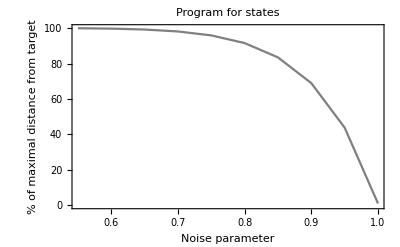

```mathematica
{noiselp, vislp, dislp} =Transpose@d[[All,2;;]] ;
plotlp = ListLinePlot[Transpose@{noiselp, 100 dislp/Max[dislp]},FrameLabel->{"Noise parameter","% of maximal distance from target"},PlotLabel->HoldForm["Program for states"],LabelStyle->{GrayLevel[0]}, PlotRange->{{0.55,1},{0,100}}, Frame-> True, PlotStyle->Gray]
```

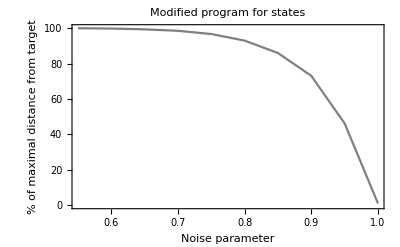

```mathematica
{noiselp2, vislp2, dislp2} =Transpose@d[[All,2;;]] ;
plotlp2 = ListLinePlot[Transpose@{noiselp2, 100 dislp2/Max[dislp2]},FrameLabel->{"Noise parameter","% of maximal distance from target"},PlotLabel->HoldForm["Modified program for states"],LabelStyle->{GrayLevel[0]}, PlotRange->{{0.55,1},{0,100}}, Frame-> True, PlotStyle->Gray]
```

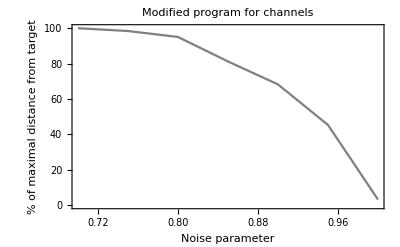

```mathematica
{noiselpch, vislpch, dislpch} =Transpose@d[[All,2;;]] ;
plotlp2 = ListLinePlot[Transpose@{noiselpch, 100 dislpch/Max[dislpch]},FrameLabel->{"Noise parameter","% of maximal distance from target"},PlotLabel->HoldForm["Modified program for channels"],LabelStyle->{GrayLevel[0]}, PlotRange->{{0.7,1},{0,100}}, Frame-> True, PlotStyle->Gray]
```

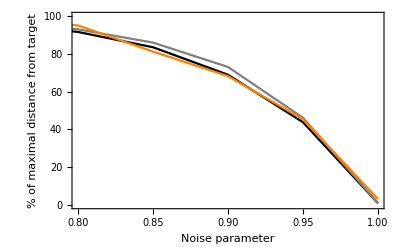

```mathematica
plotcomb = ListLinePlot[{Transpose@{noiselp, 100 dislp/Max[dislp]},Transpose@{noiselp2, 100 dislp2/Max[dislp2]},Transpose@{noiselpch, 100 dislpch/Max[dislpch]}},FrameLabel->{"Noise parameter","% of maximal distance from target"},LabelStyle->{GrayLevel[0]}, PlotRange->{{0.8,1},{0,100}}, Frame-> True, PlotStyle->{Black, Gray, Orange}]
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/distofetacomb.png", plotcomb, "PNG", RasterSize-> 2000]
```

/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/distofetacomb.png

```mathematica
bestT =Table[Transpose[ByLength[[i]]][[3]], {i, 1, Length@ByLength}]
dist=Table[Transpose[ByLength[[i]]][[4]],{i,1,Length@ByLength}];
visibility = Table[Transpose[ByLength[[i]]][[2]], {i, 1, Length@ByLength}];
plotPoints = Table[Transpose@{visibility[[i]], bestT[[i]]}, {i, 1, Length@visibility}]
plots =ListLinePlot[plotPoints, PlotLegends->Placed[{"L = 1", "L =2", "L = 3", "L = 4", "L = 5","L = 6","L = 7","L = 8","L = 9"},{0.6,0.7}], FrameLabel->{"noise parameter", "maximal visibility"},PlotRange->{{0,1},{0,1}}, Frame-> True];
distOfVis=Table[Transpose@{bestT[[i]],dist[[i]]},{i,1,Length@dist}];
plotsDist=ListLinePlot[distOfVis,FrameLabel->{"maximal visibility","distance from target"}, PlotRange->{{0,1},{0,2}}, Frame-> True];
distOfLength = Transpose@Table[Transpose@{i, dist[[i]][[v]]}, {i, 1, Length@dist}, {v, -1, - Length[dist[[1]]], -1}];
ListLinePlot@distOfLength;
```

{{0.,0.,0.},{0.148925,0.244577,0.278507},{0.425794,0.528138,0.620659},{0.476045,0.617605,0.762432},{0.490525,0.641921,0.843907},{0.47863,0.643315,0.892704},{0.439663,0.633342,0.908227},{0.399794,0.610073,0.924289},{0.36656,0.593563,0.941377},{0.335592,0.573449,0.957986},{0.0190488,0.0407778,0.0827931,0.162587,0.303438,0.968607}}

{{{0.9,0.},{0.95,0.},{1.,0.}},{{0.9,0.148925},{0.95,0.244577},{1.,0.278507}},{{0.9,0.425794},{0.95,0.528138},{1.,0.620659}},{{0.9,0.476045},{0.95,0.617605},{1.,0.762432}},{{0.9,0.490525},{0.95,0.641921},{1.,0.843907}},{{0.9,0.47863},{0.95,0.643315},{1.,0.892704}},{{0.9,0.439663},{0.95,0.633342},{1.,0.908227}},{{0.9,0.399794},{0.95,0.610073},{1.,0.924289}},{{0.9,0.36656},{0.95,0.593563},{1.,0.941377}},{{0.9,0.335592},{0.95,0.573449},{1.,0.957986}},{{0.7,0.0190488},{0.75,0.0407778},{0.8,0.0827931},{0.85,0.162587},{0.9,0.303438},{1.,0.968607}}}

{{1,0.},{2,0.278507},{3,0.620659},{4,0.762432},{5,0.843907},{6,0.892704},{7,0.908227},{8,0.924289},{9,0.941377},{10,0.957986},{11,0.968607}}

{{1,0.},{2,0.244577},{3,0.303438},{4,0.528138},{5,0.573449},{6,0.593563},{7,0.610073},{8,0.617605},{9,0.633342},{10,0.641921},{11,0.643315}}

{{1,0.},{2,0.148925},{3,0.162587},{4,0.335592},{5,0.36656},{6,0.399794},{7,0.425794},{8,0.439663},{9,0.476045},{10,0.47863},{11,0.490525}}

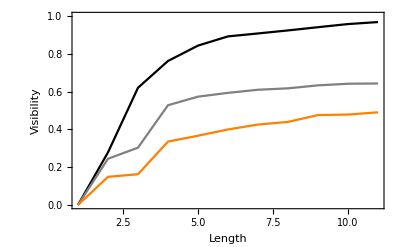

```mathematica
v = -1;
tLpoints1 = Transpose@{Transpose@Table[{i, Last[plotPoints[[i]][[v]]]}, {i, 1, Length@plotPoints}][[All,1]],Sort[Transpose@Table[{i, Last[plotPoints[[i]][[v]]]}, {i, 1, Length@plotPoints}][[All,2]]]}
tLpoints2 = Transpose@{Transpose@Table[{i, Last[plotPoints[[i]][[v-1]]]}, {i, 1, Length@plotPoints}][[All,1]],Sort[Transpose@Table[{i, Last[plotPoints[[i]][[v-1]]]}, {i, 1, Length@plotPoints}][[All,2]]]}
tLpoints3 = Transpose@{Transpose@Table[{i, Last[plotPoints[[i]][[v-2]]]}, {i, 1, Length@plotPoints}][[All,1]],Sort[Transpose@Table[{i, Last[plotPoints[[i]][[v-2]]]}, {i, 1, Length@plotPoints}][[All,2]]]}

tL = Show[ListLinePlot[{tLpoints1,tLpoints2,tLpoints3}, PlotRange->{{1,11},{0,1}}, PlotStyle->{Black,Gray, Orange}],FrameLabel->{"Length","Visibility"},LabelStyle->{GrayLevel[0]}, PlotRange->{{1,11},{0,1}}, Frame-> True]
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/tOfLcomb.png", tL, "PNG", RasterSize-> 2000];
```

```mathematica
tLpoints
```

{{1,0.40338},{2,0.722035},{3,0.760227},{4,0.745791},{5,0.722711},{6,0.70868},{7,0.681466},{8,0.650831},{9,0.619113},{10,0.591254},{11,0.562684}}

```mathematica
1 - 0.91/0.9686
```

0.0604997

```mathematica
target = {{0.59207205,-0.32598238,0.73701165},{-0.74020855,-0.58159546,0.3373989},{0.31865654,-0.74530679,-0.58564136}}
output = {{0.08821138,-0.04856733,0.10980558},{-0.11028188,-0.0866505,0.05026825},{0.04747587,-0.11104145,-0.08725329}}
Norm[ target- output, Infinity]
Norm[target, Infinity]
Norm[output, Infinity]
```

{{0.592072,-0.325982,0.737012},{-0.740209,-0.581595,0.337399},{0.318657,-0.745307,-0.585641}}

{{0.0882114,-0.0485673,0.109806},{-0.110282,-0.0866505,0.0502683},{0.0474759,-0.111041,-0.0872533}}

1.412

1.6592

0.247201

```mathematica
Det[target]
```

1.

```mathematica
t2 = target / Norm[target, Infinity]
Norm[t2, Infinity]
```

{{0.356841,-0.196469,0.444196},{-0.446123,-0.350527,0.20335},{0.192054,-0.449196,-0.352965}}

1.

```mathematica
Norm[t2 - output, Infinity]
```

0.752799